# Dimension fitter

#### Singles probability extractor

Assume that singles variable is aavailable in the context

Manually select players that have enough statistics

```mathematica
players = {"km558", "ao391", "jc632", "nawb2", "nl263", "ojp25", "ufk20", "vvt20"};
```

Estimate average number of victories and rough error on the estimate

```mathematica
findGamesBetween[p1_, p2_] := singles[ Select[#"Red Name" == p1 && #"Blue Name" == p2  || #"Red Name" == p2 && #"Blue Name" == p1 &]];

alignGamesFor[p1_, p2_]:=
Map[ If[#"Red Name"  == p1, {#"Red Score", #"Blue Score"}, { #"Blue Score", #"Red Score"}]
&]@findGamesBetween[p1,p2];

didFirstOne[scoreList_]:= If[scoreList⟦1⟧> scoreList⟦2⟧, 1, 0];

StandardError[data_]:= StandardDeviation[data] / Sqrt[Length[data]];

(*this is not accurate*)
errorFunction[data_] := If[#==0, 0.15, #] &@StandardError[data];

computeProbability[victoryList_] := If[ Length[victoryList] > 2, 
{Mean[victoryList], errorFunction[victoryList]}, 
{0.5, 0.5}   ]

probabilityBetween[p1_, p2_]:= computeProbability@N[didFirstOne/@alignGamesFor[p1,p2]];
```

Create a network of probabilities in a format {“p1, p2, probability, error}

```mathematica
allPlayerCombos = DeleteDuplicates[Map[Sort,#]] &@Permutations[ players, {2}];

allLenghs = Join[#, N[probabilityBetween@@#]] &/@allPlayerCombos;
```

Select the games with suficient statistics for further analysis

```mathematica
n = Length[players];
lengthsBetweenPlayers = Select[#⟦4⟧< 0.5&]@ allLenghs
playerMap = <|Thread[ players -> Range@Length@players]|>;
lengths = {playerMap[#⟦1⟧], playerMap[#⟦2⟧], Abs[0.5- #⟦3⟧], #⟦4⟧} &/@ lengthsBetweenPlayers;
```

(ao391 | km558 | 0.1 | 0.1
jc632 | km558 | 0.4 | 0.244949
km558 | nawb2 | 0.8 | 0.2
km558 | nl263 | 0.846154 | 0.104154
km558 | ufk20 | 0.470588 | 0.124784
km558 | vvt20 | 0.733333 | 0.118187
ao391 | ufk20 | 0.222222 | 0.146986
ao391 | vvt20 | 0. | 0.1
jc632 | nawb2 | 0.428571 | 0.202031
jc632 | nl263 | 0.75 | 0.25
jc632 | ufk20 | 0.916667 | 0.0833333
jc632 | vvt20 | 0.666667 | 0.166667
nawb2 | nl263 | 0.75 | 0.163663
nawb2 | ufk20 | 1. | 0.1
nawb2 | vvt20 | 0.714286 | 0.184428
nl263 | ojp25 | 0.333333 | 0.333333
nl263 | ufk20 | 0.4 | 0.244949
nl263 | vvt20 | 0.714286 | 0.184428
ufk20 | vvt20 | 0.55 | 0.0796628)

#### Training lenghts

```mathematica
n = 4; (*number of players*)
lengths = {
{1,2,1.2},
{1,3, 1.3}
};
lengths = {#⟦1⟧,#⟦2⟧, RandomReal[]}&/@ Permutations[Range[n ], {2}];
```

#### Parameters

```mathematica
d = 2; (*dimensions*)
δ = 0.00001; (*sensitivity of gradient search function*)
```

#### Costing function

```mathematica
costFunction[xi_]:= Total[(Norm[ xi⟦ #⟦2⟧ ⟧ - xi⟦ #⟦1⟧ ⟧ ] - #⟦3⟧)^2 &/@ lengths]
```

```mathematica
(* with error weighting*)
costFunction[xi_]:= Total[1/#⟦4⟧*( Norm[ xi⟦ #⟦2⟧ ⟧ - xi⟦ #⟦1⟧ ⟧ ] - #⟦3⟧)^2 &/@ lengths]
```

## Algorithm

```mathematica
(* to do *)
range = Max[lengths⟦All, 3⟧] * Table[ {-1,1}, {d}];
```

Gradient desent

```mathematica
(* return: list of x *)
guessValues[]:= {Table[0,{d}] } ~ Join ~ Table[RandomReal/@range, {n-1}]
```

```mathematica
(* return: gradient direction for i point *)
findGradientFor[xi0_, i_]:= 
Normalize/@(
costFunction/@ 
(ReplacePart[xi0, i-> (#+ xi0⟦i⟧)]&/@ 
(δ ×IdentityMatrix[d]))  
- costFunction[xi0]*ConstantArray[1, {d}]
);

(* return: list of vector pointing at the gradient descent direction*)
findGradients[ xi0_]:={Table[0,{d}] } ~ Join ~( findGradientFor[xi0, #]&/@Range[2,n])
```

```mathematica
(* return: new xi *)
doStep[xi0_, stepSize_] := xi0 + stepSize*findGradients[xi0]
```

```mathematica
(* alternative method: iterate each coordinate 1 by 1 *)
doStepFor[xi0_, stepSize_, i_]:= xi0 + stepSize* ReplacePart[ ConstantArray[0, {n,d}], i->findGradientFor[xi0, i]]

(* return: new xi *)
doStep[xi0_, stepSize_] := Fold[ doStepFor[#1, stepSize, #2]&,xi0, Range[2,n]]
```

#### RUN

```mathematica
accumulatedXs = {};
bestX = guessValues[];
```

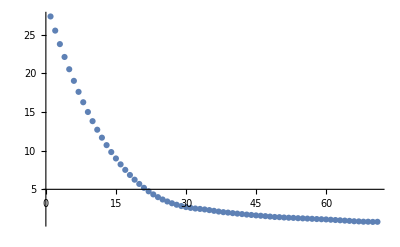

```mathematica
Do[
Clear[x, cost, step];
Dynamic[x];
x = guessValues[];
cost = {costFunction[x]};
step = -0.01;

For[ stepsDone = 0,stepsDone<1000, stepsDone++,
x = doStep[x, step];
AppendTo[cost, costFunction[x]];
If[cost⟦-1⟧≥   cost⟦-2⟧ , Break[]];
(*step = -0.000001*Abs[cost⟦-1⟧-   cost⟦-2⟧];*)
];
accumulatedXs = accumulatedXs ~ Join ~ {x};
If[ costFunction[ bestX] > costFunction[x], bestX = x];

, {100}]
(*end Do*)

ListPlot[cost, PlotRange->{5,0}]
```

```mathematica
Transpose[ { players} ~Join~ Transpose@bestX ~Join~ Transpose@x]
"best cost" -> costFunction[ bestX]
```

(km558 | 0. | 0. | 0. | 0.
ao391 | -0.396884 | -0.0487367 | 0.175816 | -0.398789
jc632 | 0.25659 | -0.0702752 | -0.113533 | -0.086046
nawb2 | 0.336385 | -0.154027 | -0.153348 | -0.166975
nl263 | 0.0933743 | -0.306137 | 0.170166 | -0.184062
ojp25 | 0.125313 | -0.124652 | 0.173475 | 0.0355665
ufk20 | -0.0812174 | -0.112715 | 0.199497 | -0.018025
vvt20 | 0.0694595 | -0.139654 | 0.130949 | 0.0155798)

best cost→0.740259

```mathematica
(*normalsie with respecto to players*)
findTransform[x0_, x1_]:=( 1/(x1-x0))*( # - x0)&
normaliseX[x_]:= findTransform[x⟦playerMap["ao391"]⟧, x⟦playerMap["nawb2"]⟧]/@ x
```

```mathematica
(*normalise with respect to mean*)
transform[x_] := ( # - Mean[x] +{1,1}*0.5)/ StandardDeviation[x]/6&
normaliseX[x_]:= transform[x]/@ x
```

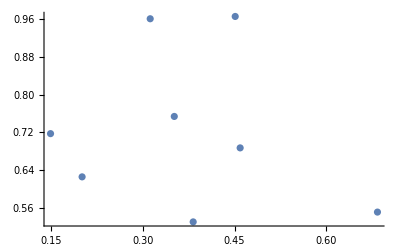

```mathematica
ListPlot[
Tooltip[#⟦{2,3}⟧,#⟦1⟧]&/@Transpose[ { players} ~Join~ Transpose@normaliseX@bestX ],
PlotRange->All
]
```

```mathematica
findDistanceBetween[p1_, p2_, x_]:=Abs@ Norm[ x⟦ playerMap[p1] ⟧ -x⟦ playerMap[p2] ⟧ ]

Transpose[
Transpose@lengthsBetweenPlayers 
~Join~
{findDistanceBetween[#⟦1⟧,#⟦2⟧, bestX]&/@ lengthsBetweenPlayers}
]
```

(ao391 | km558 | 0.1 | 0.1 | 0.399865
jc632 | km558 | 0.4 | 0.244949 | 0.26604
km558 | nawb2 | 0.8 | 0.2 | 0.369972
km558 | nl263 | 0.846154 | 0.104154 | 0.32006
km558 | ufk20 | 0.470588 | 0.124784 | 0.138928
km558 | vvt20 | 0.733333 | 0.118187 | 0.155974
ao391 | ufk20 | 0.222222 | 0.146986 | 0.322084
ao391 | vvt20 | 0. | 0.1 | 0.475123
jc632 | nawb2 | 0.428571 | 0.202031 | 0.115679
jc632 | nl263 | 0.75 | 0.25 | 0.286827
jc632 | ufk20 | 0.916667 | 0.0833333 | 0.340463
jc632 | vvt20 | 0.666667 | 0.166667 | 0.199578
nawb2 | nl263 | 0.75 | 0.163663 | 0.286691
nawb2 | ufk20 | 1. | 0.1 | 0.419641
nawb2 | vvt20 | 0.714286 | 0.184428 | 0.267313
nl263 | ojp25 | 0.333333 | 0.333333 | 0.184273
nl263 | ufk20 | 0.4 | 0.244949 | 0.260565
nl263 | vvt20 | 0.714286 | 0.184428 | 0.168191
ufk20 | vvt20 | 0.55 | 0.0796628 | 0.153066)

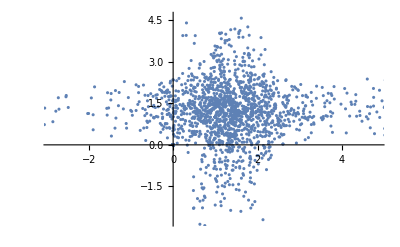

```mathematica
findTransform[x0_, x1_]:=( 1/(x1-x0))*( # - x0)&
normaliseX[x_]:= findTransform[x⟦playerMap["ao391"]⟧, x⟦playerMap["ufk20"]⟧]/@ x
Flatten[ normaliseX/@accumulatedXs, 1] //ListPlot
```

## Testing

#### Test gradient finding algorithm

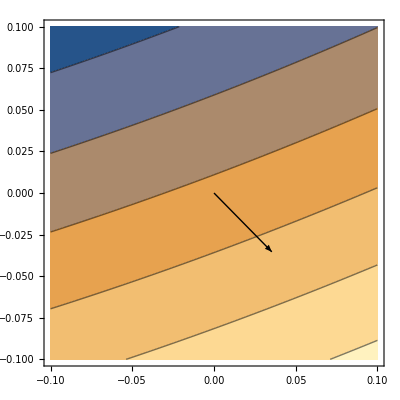

```mathematica
Module[ {i = 3},
Show[
ContourPlot[
costFunction[ReplacePart[x, i-> (x⟦i⟧ + {dx,dy})]],
{dx, -0.1,0.1},{dy,-0.1,0.1}
],

Graphics[ Arrow[{ {0,0}, 0.05Normalize[findGradientFor[x, i]]}]]
]]
```

```mathematica
?For
```

For[start,test,incr,body] executes start, then repeatedly evaluates body and incr until test fails to give True.